## Analytic Expression

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1]; 

mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalmu[μ_,T_,chem_,c_,d_]:=Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(chem/3)^2/T^2]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalT[μ_,T_,c_,d_]:=1/T mDcal[μ,T,c,d];
```

NDSolve::precw: The precision of the differential equation ({{as'[t]==1/12 as[t]^2 (-33.+2 If[«3»])+1/96 as[t]^3 (-612.+76. If[«3»])+1/128 as[t]^4 (-2857+5033/9 If[«3»]-325/27 Power[«2»])+1/256 as[t]^5 (-149753/6-1093/729 Power[«2»]-3564 Zeta[«1»]-Power[«2»] Plus[«2»]+If[«3»] Plus[«2»]),as[10000 Log[4]]==0.0000376185},{},{},{},{}}) is less than WorkingPrecision (32.).

NDSolve::ndsz: At t == 2.05914, step size is effectively zero; singularity or stiff system suspected.

## Plots

```mathematica
kfinal={0.47034270691413915,-0.25481763807967805};
kfinalu={0.8016955527941704,-0.36040626803845205};
kfinall={0.1389898610341079,-0.14922900812090412};
```

```mathematica
(*mDcalmu[μ_,T_,chem_,c_,d_]*)
mDcalmu[2π,0.5,0.1,kfinal[[1]],kfinal[[2]]]
```

0.975907

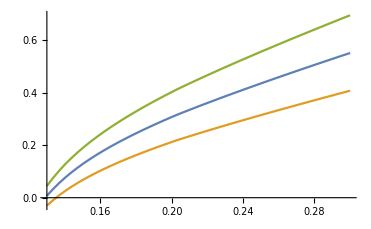

```mathematica
Plot[{mDcalmu[2π,T,0.155,kfinal[[1]],kfinal[[2]]],mDcalmu[2π,T,0.155,kfinall[[1]],kfinall[[2]]],mDcalmu[2π,T,0.155,kfinalu[[1]],kfinalu[[2]]]},{T,0.13,0.3}]
```

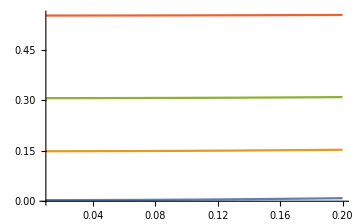

```mathematica
Plot[{mDcalmu[2π,0.13,x,kfinal[[1]],kfinal[[2]]],mDcalmu[2π,0.155,x,kfinal[[1]],kfinal[[2]]],mDcalmu[2π,0.2,x,kfinal[[1]],kfinal[[2]]],mDcalmu[2π,0.3,x,kfinal[[1]],kfinal[[2]]]},{x,0.01,0.2}]
```

## Interpolation at Tc=155MeV

```mathematica
chemD=Table[{x,mDcalmu[2π,0.155,x,kfinall[[1]],kfinall[[2]]]},{x,0,1.,0.01}]
```

{{0.,0.0831374},{0.01,0.0831485},{0.02,0.0831818},{0.03,0.0832374},{0.04,0.0833152},{0.05,0.0834152},{0.06,0.0835373},{0.07,0.0836817},{0.08,0.0838482},{0.09,0.0840368},{0.1,0.0842476},{0.11,0.0844804},{0.12,0.0847353},{0.13,0.0850121},{0.14,0.085311},{0.15,0.0856317},{0.16,0.0859744},{0.17,0.0863389},{0.18,0.0867251},{0.19,0.0871331},{0.2,0.0875628},{0.21,0.0880141},{0.22,0.088487},{0.23,0.0889813},{0.24,0.0894971},{0.25,0.0900342},{0.26,0.0905927},{0.27,0.0911723},{0.28,0.0917731},{0.29,0.0923949},{0.3,0.0930377},{0.31,0.0937014},{0.32,0.094386},{0.33,0.0950912},{0.34,0.0958171},{0.35,0.0965635},{0.36,0.0973303},{0.37,0.0981175},{0.38,0.098925},{0.39,0.0997526},{0.4,0.1006},{0.41,0.101468},{0.42,0.102355},{0.43,0.103262},{0.44,0.104189},{0.45,0.105136},{0.46,0.106101},{0.47,0.107086},{0.48,0.108091},{0.49,0.109114},{0.5,0.110156},{0.51,0.111217},{0.52,0.112297},{0.53,0.113395},{0.54,0.114512},{0.55,0.115647},{0.56,0.1168},{0.57,0.117972},{0.58,0.119161},{0.59,0.120368},{0.6,0.121593},{0.61,0.122836},{0.62,0.124096},{0.63,0.125373},{0.64,0.126668},{0.65,0.12798},{0.66,0.129308},{0.67,0.130654},{0.68,0.132016},{0.69,0.133395},{0.7,0.13479},{0.71,0.136201},{0.72,0.137629},{0.73,0.139073},{0.74,0.140532},{0.75,0.142008},{0.76,0.143499},{0.77,0.145005},{0.78,0.146527},{0.79,0.148064},{0.8,0.149617},{0.81,0.151184},{0.82,0.152766},{0.83,0.154363},{0.84,0.155975},{0.85,0.157601},{0.86,0.159241},{0.87,0.160896},{0.88,0.162564},{0.89,0.164247},{0.9,0.165944},{0.91,0.167654},{0.92,0.169378},{0.93,0.171115},{0.94,0.172866},{0.95,0.17463},{0.96,0.176407},{0.97,0.178196},{0.98,0.179999},{0.99,0.181815},{1.,0.183643}}

```mathematica
tempmD=Table[{x,mDcalmu[2π,x,0,kfinall[[1]],kfinall[[2]]]},{x,0.155,0.2,0.000001}];
```

```mathematica
res=Range[Length[chemD]];
Do[res[[i]]=Position[tempmD[[All,2]],Nearest[tempmD[[All,2]],chemD[[i,2]]][[1]]][[1,1]],{i,1,Length[chemD]}]
res
```

{1,4,13,29,51,78,113,153,199,252,311,376,448,526,610,700,797,899,1009,1124,1246,1374,1509,1650,1798,1952,2112,2279,2453,2633,2819,3012,3212,3418,3632,3851,4078,4311,4551,4798,5051,5312,5579,5854,6135,6423,6719,7021,7330,7647,7971,8302,8640,8985,9338,9698,10065,10440,10822,11212,11609,12014,12426,12846,13273,13708,14151,14602,15060,15526,16000,16482,16972,17469,17975,18489,19010,19540,20077,20623,21177,21739,22309,22887,23474,24068,24671,25283,25902,26530,27166,27811,28463,29124,29794,30472,31158,31853,32556,33267,33987}

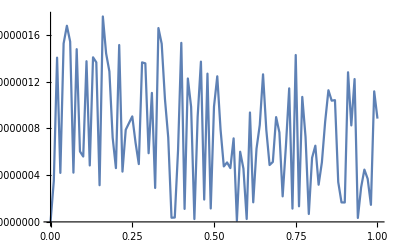

```mathematica
mDdiff=Range[res];
Do[mDdiff[[i]]={chemD[[i,1]],chemD[[i,2]]-tempmD[[res[[i]],2]]},{i,Length[res]}];
ListPlot[Abs[mDdiff],Joined->True]
```

```mathematica
chemTl=chemD[[All,1]];
Do[chemTl[[i]]=Append[{chemTl[[i]]},tempmD[[res[[i]],1]]],{i,Length[res]}];
```

```mathematica
chemTu
```

{{0.,0.155},{0.01,0.155002},{0.02,0.155008},{0.03,0.155019},{0.04,0.155034},{0.05,0.155053},{0.06,0.155076},{0.07,0.155103},{0.08,0.155135},{0.09,0.155171},{0.1,0.155211},{0.11,0.155255},{0.12,0.155304},{0.13,0.155356},{0.14,0.155413},{0.15,0.155474},{0.16,0.15554},{0.17,0.15561},{0.18,0.155683},{0.19,0.155762},{0.2,0.155844},{0.21,0.155931},{0.22,0.156022},{0.23,0.156117},{0.24,0.156216},{0.25,0.15632},{0.26,0.156428},{0.27,0.156541},{0.28,0.156657},{0.29,0.156778},{0.3,0.156904},{0.31,0.157033},{0.32,0.157167},{0.33,0.157305},{0.34,0.157448},{0.35,0.157595},{0.36,0.157746},{0.37,0.157901},{0.38,0.158061},{0.39,0.158226},{0.4,0.158394},{0.41,0.158568},{0.42,0.158745},{0.43,0.158927},{0.44,0.159113},{0.45,0.159304},{0.46,0.159499},{0.47,0.159699},{0.48,0.159903},{0.49,0.160111},{0.5,0.160324},{0.51,0.160542},{0.52,0.160764},{0.53,0.16099},{0.54,0.161221},{0.55,0.161456},{0.56,0.161696},{0.57,0.161941},{0.58,0.162189},{0.59,0.162443},{0.6,0.162701},{0.61,0.162964},{0.62,0.163231},{0.63,0.163503},{0.64,0.163779},{0.65,0.16406},{0.66,0.164345},{0.67,0.164636},{0.68,0.16493},{0.69,0.16523},{0.7,0.165534},{0.71,0.165843},{0.72,0.166156},{0.73,0.166474},{0.74,0.166797},{0.75,0.167124},{0.76,0.167456},{0.77,0.167793},{0.78,0.168134},{0.79,0.168481},{0.8,0.168832},{0.81,0.169187},{0.82,0.169548},{0.83,0.169913},{0.84,0.170282},{0.85,0.170657},{0.86,0.171036},{0.87,0.171421},{0.88,0.171809},{0.89,0.172203},{0.9,0.172601},{0.91,0.173005},{0.92,0.173413},{0.93,0.173825},{0.94,0.174243},{0.95,0.174665},{0.96,0.175093},{0.97,0.175525},{0.98,0.175961},{0.99,0.176403},{1.,0.176849}}

```mathematica
chemTl
```

{{0.,0.155},{0.01,0.155003},{0.02,0.155012},{0.03,0.155028},{0.04,0.15505},{0.05,0.155077},{0.06,0.155112},{0.07,0.155152},{0.08,0.155198},{0.09,0.155251},{0.1,0.15531},{0.11,0.155375},{0.12,0.155447},{0.13,0.155525},{0.14,0.155609},{0.15,0.155699},{0.16,0.155796},{0.17,0.155898},{0.18,0.156008},{0.19,0.156123},{0.2,0.156245},{0.21,0.156373},{0.22,0.156508},{0.23,0.156649},{0.24,0.156797},{0.25,0.156951},{0.26,0.157111},{0.27,0.157278},{0.28,0.157452},{0.29,0.157632},{0.3,0.157818},{0.31,0.158011},{0.32,0.158211},{0.33,0.158417},{0.34,0.158631},{0.35,0.15885},{0.36,0.159077},{0.37,0.15931},{0.38,0.15955},{0.39,0.159797},{0.4,0.16005},{0.41,0.160311},{0.42,0.160578},{0.43,0.160853},{0.44,0.161134},{0.45,0.161422},{0.46,0.161718},{0.47,0.16202},{0.48,0.162329},{0.49,0.162646},{0.5,0.16297},{0.51,0.163301},{0.52,0.163639},{0.53,0.163984},{0.54,0.164337},{0.55,0.164697},{0.56,0.165064},{0.57,0.165439},{0.58,0.165821},{0.59,0.166211},{0.6,0.166608},{0.61,0.167013},{0.62,0.167425},{0.63,0.167845},{0.64,0.168272},{0.65,0.168707},{0.66,0.16915},{0.67,0.169601},{0.68,0.170059},{0.69,0.170525},{0.7,0.170999},{0.71,0.171481},{0.72,0.171971},{0.73,0.172468},{0.74,0.172974},{0.75,0.173488},{0.76,0.174009},{0.77,0.174539},{0.78,0.175076},{0.79,0.175622},{0.8,0.176176},{0.81,0.176738},{0.82,0.177308},{0.83,0.177886},{0.84,0.178473},{0.85,0.179067},{0.86,0.17967},{0.87,0.180282},{0.88,0.180901},{0.89,0.181529},{0.9,0.182165},{0.91,0.18281},{0.92,0.183462},{0.93,0.184123},{0.94,0.184793},{0.95,0.185471},{0.96,0.186157},{0.97,0.186852},{0.98,0.187555},{0.99,0.188266},{1.,0.188986}}

```mathematica
mDcalmu[2π,0.155,0,kfinall[[1]],kfinall[[2]]]
```

0.0831374

```mathematica
mDcalmu[2π,0.155,0,kfinal[[1]],kfinal[[2]]]
```

0.14846

```mathematica
mDcalmu[2π,0.155,0,kfinalu[[1]],kfinalu[[2]]]
```

0.213784